```mathematica
dx=10^-4;
n=100;
α[x]=1/x(1/2-1/π∑_(k=1)^n Sin[(2π k x)/dx]/k);
Φ[x,y]=-1/(√(x^2+y^2));
RealForce[x,y]=-{D[Φ[x,y],x],D[Φ[x,y],y]};
AnalyticFx[x_,y_]:=-((x(1+α[x]dx-dx/2))/((√(x^2+y^2))^3)+dx/((√(x^2+y^2))^5)(3/2 x^2+3x y))
AnalyticFy[x_,y_]:=-((y(1+α[y]dx-dx/2))/((√(x^2+y^2))^3)+dx/((√(x^2+y^2))^5)(3/2 y^2+3x y))
ForceAnalytic[x,y]={AnalyticFx[x,y],AnalyticFy[x,y]};
```

```mathematica
RealForce[x,y];
```

```mathematica
{-x/((x^2+y^2)^(3/2)),-y/((x^2+y^2)^(3/2))}-ForceAnalytic[x,y]//Simplify;
```

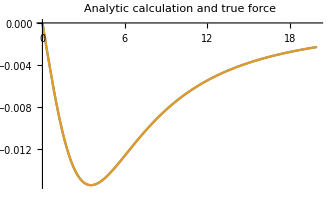

```mathematica
Plot[{ForceAnalytic[x,y][[1]]/.y->5,RealForce[x,y][[1]]/.y->5},{x,0,20},PlotLabel->"Analytic calculation and true force "]
```

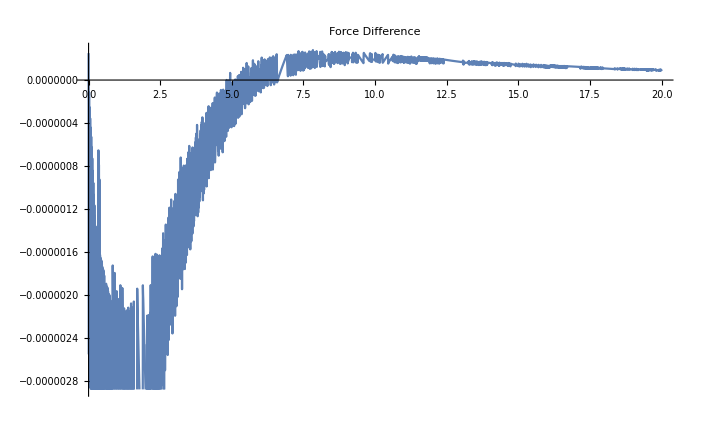

```mathematica
Plot[{((ForceAnalytic[x,y][[1]]-RealForce[x,y][[1]]))/.y->3},{x,0,20},PlotLabel->"Force Difference"]
```

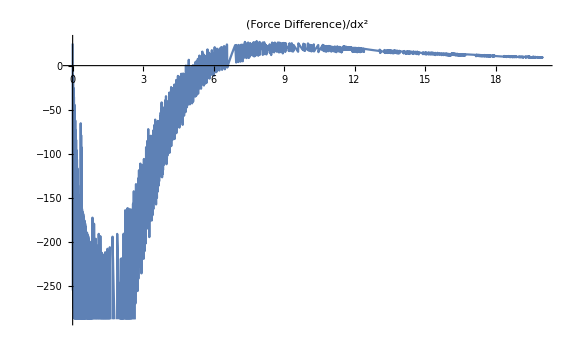

```mathematica
Plot[{((ForceAnalytic[x,y][[1]]-RealForce[x,y][[1]])/dx^2)/.y->3},{x,0,20},PlotLabel->"(Force Difference)/dx^2"]
```

```mathematica
Plot3D[{((ForceAnalytic[x,y][[1]]-RealForce[x,y][[1]])/dx^2)},{x,0,20},{y,0,20},PlotLabel->"(The difference between the forces in direction x)/dx^2 "]
```

-Graphics3D-

```mathematica
dx=10^-4;
n=400;
α[x]=1/x(1/2-1/π∑_(k=1)^n Sin[(2π k x)/dx]/k);
Φ[x,y]=-1/(√(x^2+y^2));
RealForce[x,y]=-{D[Φ[x,y],x],D[Φ[x,y],y]};
AnalyticFx[x_,y_]:=-((x(1+α[x]dx-dx/2))/((√(x^2+y^2))^3)+dx/((√(x^2+y^2))^5)(3/2 x^2+3x y))
AnalyticFy[x_,y_]:=-((y(1+α[y]dx-dx/2))/((√(x^2+y^2))^3)+dx/((√(x^2+y^2))^5)(3/2 y^2+3x y))
ForceAnalyticn400[x,y]={AnalyticFx[x,y],AnalyticFy[x,y]};
```

```mathematica
dx=10^-4;
n=0;
αn1[x]=1/x(1/2-1/π∑_(k=1)^n Sin[(2π k x)/dx]/k);
Φ[x,y]=-1/(√(x^2+y^2));
RealForce[x,y]=-{D[Φ[x,y],x],D[Φ[x,y],y]};
AnalyticFx[x_,y_]:=-((x(1+αn1[x]dx-dx/2))/((√(x^2+y^2))^3)+dx/((√(x^2+y^2))^5)(3/2 x^2+3x y))
AnalyticFy[x_,y_]:=-((y(1+αn1[y]dx-dx/2))/((√(x^2+y^2))^3)+dx/((√(x^2+y^2))^5)(3/2 y^2+3x y))
ForceAnalyticn1[x,y]={AnalyticFx[x,y],AnalyticFy[x,y]};
```

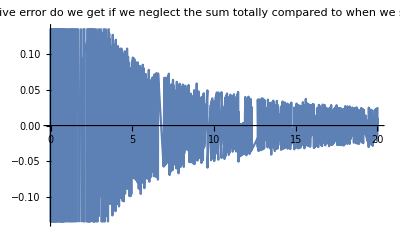

```mathematica
Plot[{((ForceAnalyticn400[x,y][[1]]-ForceAnalyticn1[x,y][[1]])/(ForceAnalyticn1[x,y][[1]] dx))/.y->3},{x,0,20},PlotLabel->"How much relative error do we get if we neglect the sum totally compared to when we sum over 400 terms?",PlotLegends->"(The relative difference)/dx"]
```